Problem II : already producing

## Benchmark Model

```mathematica
Solve[x==((theta -alfa k) k/(r-mu)x+(delta k+(1-alfa k0)k0/r))/((theta -alfa k) k/(r-mu))/d1,x]
```

{{x→((mu-r) (k0-alfa k0^2+delta k r))/((-1+d1) k r (alfa k-theta))}}

```mathematica
xx=d1/(d1-1) (delta k+(1-alfa k0)/r k0)/(theta -alfa k) (r-mu)/k
a=(delta k+(1-alfa k0)/r k0)xx^(-d1)/(d1-1)
```

(d1 (delta k+(k0 (1-alfa k0))/r) (-mu+r))/((-1+d1) k (-alfa k+theta))

((delta k+(k0 (1-alfa k0))/r) ((d1 (delta k+(k0 (1-alfa k0))/r) (-mu+r))/((-1+d1) k (-alfa k+theta)))^-d1)/(-1+d1)

```mathematica
kk=(theta -alfa k) k/(r-mu);
jj=(delta k+(1-alfa k0)k0/r);
xx1=d1/(d1-1) jj/kk
a1=jj xx1^(-d1)/(d1-1)
```

(d1 (delta k+(k0 (1-alfa k0))/r) (-mu+r))/((-1+d1) k (-alfa k+theta))

((delta k+(k0 (1-alfa k0))/r) ((d1 (delta k+(k0 (1-alfa k0))/r) (-mu+r))/((-1+d1) k (-alfa k+theta)))^-d1)/(-1+d1)

```mathematica
a xx^d1
```

(delta k+(k0 (1-alfa k0))/r)/(-1+d1)

```mathematica
aB[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:= (δ  k + (1-  α k0)k0/r  )xx^(-d1[μ,σ,r])/(d1[μ,σ,r]-1);
hB[xx_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=(θ- α k) k/(r-μ)xx-( δ  k + (1-  α k0)k0/r  );
d1[μ_,σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2];
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
xxB[r,μ,σ,θ,k0,α,δ,k]
hB[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]-aB[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]* xxB[r,μ,σ,θ,k0,α,δ,k]^d1[μ,σ,r];

F[y_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=hB[y,r,μ,σ,θ,k0,α,δ,k]-aB[y,r,μ,σ,θ,k0,α,δ,k]* y^d1[μ,σ,r];
```

(((k0 (1-k0 α))/r+k δ) (r-μ) (1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))/(k (-k α+θ) (-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))

```mathematica
Manipulate[Show[Plot[{
(* hB[x,r,μ,σ,θ,k0,α,δ,k]-aB[x,r,μ,σ,θ,k0,α,δ,k]* x^d1[μ,σ,r], *)
(* hB[x,r,μ,σ,θ,k0,α,δ,k]-aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],*)
aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*x ^d1[μ,σ,r],
hB[x,r,μ,σ,θ,k0,α,δ,k]
(*aB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]*)
(*, aB[x,r,μ,σ,θ,k0,α,δ,k]* x^d1[μ,σ,r]} *) }
,{x,0.01,1},AxesLabel->{"x","F(x)"},PlotLegends->"Placeholder"],
Epilog->{Black, PointSize[0.02],Point[{xxB[r,μ,σ,θ,k0,α,δ,k] ,hB[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]
}]}],
{r,0.001,1},{μ,-r,r},{k0,0.001,10},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]}]
```

## Capacity Optimization Model

```mathematica
h[k_]:=(θ-α k)k x/(r-μ)-(δ  k+(1-α k0)/r k0);
D[h[k],k]
```

-δ-(k x α)/(r-μ)+(x (-k α+θ))/(r-μ)

```mathematica
D[h[k],{k,2}]
```

-(2 x α)/(r-μ)

Capacidade optimal:

```mathematica
Solve[-δ-(k x α)/(r-μ)+(x (-k α+θ))/(r-μ)==0,k]
```

{{k→(-r δ+x θ+δ μ)/(2 x α)}}

```mathematica
Kopt=θ/(2 α) -δ (r-μ)/(2 α x);
Simplify[h[Kopt]-(k0/r(k0  α-1)+(θ x -δ (r-μ))^2/(4 α x(r-μ)))] (*verifiação de maneira alternativa de escrever fórmula de h[Kopt]*)
Simplify[h[Kopt]]
```

0

(4 k0^2 x α^2 (r-μ)+4 k0 x α (-r+μ)+r (-r δ+x θ+δ μ)^2)/(4 r x α (r-μ))

```mathematica
D[h[Kopt],x]
```

(δ (θ-α (θ/(2 α)-(δ (r-μ))/(2 x α))))/(2 x α)-(δ (θ/(2 α)-(δ (r-μ))/(2 x α)))/(2 x)+((θ-α (θ/(2 α)-(δ (r-μ))/(2 x α))) (θ/(2 α)-(δ (r-μ))/(2 x α)))/(r-μ)-(δ^2 (r-μ))/(2 x^2 α)

```mathematica
Simplify[D[h[Kopt],x]]
```

-(r^2 δ^2-x^2 θ^2-2 r δ^2 μ+δ^2 μ^2)/(4 r x^2 α-4 x^2 α μ)

```mathematica
Simplify[-(r^2 δ^2-x^2 θ^2-2 r δ^2 μ+δ^2 μ^2)/(4 r x^2 α-4 x^2 α μ)-(-(δ(r-μ))^2+(x θ)^2)/(4 x^2 α (r-μ))] (*verifiação de maneira alternativa de escrever a derivada em ordem a x de h[Kopt]*)
```

0

```mathematica
a=(k0/r(k0  α-1)+(θ x -δ (r-μ))^2/(4 α x(r-μ)))*(x^(-d1));
Solve[a d1 x^(d1-1)==(-(δ(r-μ))^2+(x θ)^2)/(4 x^2 α (r-μ)),x]
```

{{x→1/(2 (-r θ^2+d1 r θ^2))(4 d1 k0 r α-4 d1 k0^2 r α^2+2 d1 r^2 δ θ-4 d1 k0 α μ+4 d1 k0^2 α^2 μ-2 d1 r δ θ μ-√((-4 d1 k0 r α+4 d1 k0^2 r α^2-2 d1 r^2 δ θ+4 d1 k0 α μ-4 d1 k0^2 α^2 μ+2 d1 r δ θ μ)^2-4 (-r θ^2+d1 r θ^2) (r^3 δ^2+d1 r^3 δ^2-2 r^2 δ^2 μ-2 d1 r^2 δ^2 μ+r δ^2 μ^2+d1 r δ^2 μ^2)))},{x→1/(2 (-r θ^2+d1 r θ^2))(4 d1 k0 r α-4 d1 k0^2 r α^2+2 d1 r^2 δ θ-4 d1 k0 α μ+4 d1 k0^2 α^2 μ-2 d1 r δ θ μ+√((-4 d1 k0 r α+4 d1 k0^2 r α^2-2 d1 r^2 δ θ+4 d1 k0 α μ-4 d1 k0^2 α^2 μ+2 d1 r δ θ μ)^2-4 (-r θ^2+d1 r θ^2) (r^3 δ^2+d1 r^3 δ^2-2 r^2 δ^2 μ-2 d1 r^2 δ^2 μ+r δ^2 μ^2+d1 r δ^2 μ^2)))}}

```mathematica
Simplify[(4 d1 k0 r α-4 d1 k0^2 r α^2+2 d1 r^2 δ θ-4 d1 k0 α μ+4 d1 k0^2 α^2 μ-2 d1 r δ θ μ-√((-4 d1 k0 r α+4 d1 k0^2 r α^2-2 d1 r^2 δ θ+4 d1 k0 α μ-4 d1 k0^2 α^2 μ+2 d1 r δ θ μ)^2-4 (-r θ^2+d1 r θ^2) (r^3 δ^2+d1 r^3 δ^2-2 r^2 δ^2 μ-2 d1 r^2 δ^2 μ+r δ^2 μ^2+d1 r δ^2 μ^2)))/(2 (-r θ^2+d1 r θ^2))]
(*valor do menor threshold *)
```

-1/((-1+d1) r θ^2)(d1 (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2))

```mathematica
Simplify[(4 d1 k0 r α-4 d1 k0^2 r α^2+2 d1 r^2 δ θ-4 d1 k0 α μ+4 d1 k0^2 α^2 μ-2 d1 r δ θ μ+√((-4 d1 k0 r α+4 d1 k0^2 r α^2-2 d1 r^2 δ θ+4 d1 k0 α μ-4 d1 k0^2 α^2 μ+2 d1 r δ θ μ)^2-4 (-r θ^2+d1 r θ^2) (r^3 δ^2+d1 r^3 δ^2-2 r^2 δ^2 μ-2 d1 r^2 δ^2 μ+r δ^2 μ^2+d1 r δ^2 μ^2)))/(2 (-r θ^2+d1 r θ^2))]
(*valor do maior threshold *)
```

1/((-1+d1) r θ^2)(-d1 (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2))

Afinal temos 2 raízes possíveis, dados que os níveis de procura para ambas são >0. Isto levanta-me algumas questões sobre como proceder de modo a seleccionar a raíz associada ao optimal stopping time. Parece-me que a melhor solução é verificar para qual a (menor) raíz se verificam os supostos da HJB.

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
```

```mathematica
hC[x_,r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=(θ-α k)k x/(r-μ)-(δ  k+(1-α k0)/r k0);
Kopt[x_,r_,μ_,θ_,α_,δ_]:=θ/(2 α) -δ (r-μ)/(2 α x);
d1[μ_, σ_,r_]:=1/2-μ/σ^2+Sqrt[(1/2-μ/σ^2)^2+2r/σ^2];
aC[x_,r_,μ_, σ_,θ_,k0_,α_,δ_]:=(k0/r(k0  α-1)+(θ x -δ (r-μ))^2/(4 α x(r-μ)))*(x^(-d1[μ,σ,r])); (* usar apenas com xNeg e xPos !! *)
```

```mathematica
xNeg[r_,μ_, σ_,θ_,k0_,α_,δ_]:=-1/((-1+d1[μ,σ,r]) r θ^2)(d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2)) ;
xPos[r_,μ_, σ_,θ_,k0_,α_,δ_]:=1/((-1+d1[μ,σ,r]) r θ^2)(-d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2));
F[y_,r_,μ_, σ_,θ_,k0_,α_,δ_]:=hC[y,r,μ,σ,θ,k0,α,δ,Kopt[y,r,μ,θ,α,δ]]-aC[y,r,μ,σ,θ,k0,α,δ]* y^d1[μ,σ,r];
```

Análise de xNeg:

```mathematica
Manipulate[Show[Plot[{
xPos[r,μ,σ,θ,k0,α,δ],
xNeg[r,μ,σ,θ,k0,α,δ],
Sqrt[((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2)],
-d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) ,
aC[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]
}
,{μ,-r,r}
,AxesLabel->{"μ","x"},PlotLegends->"Placeholder",AxesOrigin->{0,0}] 
],
{r,0.001,1},{σ,0.001,1},{θ,1,10},{k0,0.001,10},{α,0.001,Min[1/k0,θ/k]},{δ,0.001,1}]
```

Indica que os 2 pares de raízes obtidos diferem entre si - o que é uma bela porcaria. Possivelmente deve-se a não se conseguir ismplificar as fórmulas mais, pois o resultado deveria ser igual.

```mathematica
Simplify@aC[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)
```

(-1/((-1+dd1) r θ^2)(dd1 (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 dd1^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2)))^-dd1 ((k0 (-1+k0 α))/r-((-1+dd1) r θ^2 (-1/((-1+dd1) r θ)(dd1 (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 dd1^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2))+δ (-r+μ))^2)/(4 α (dd1 (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 dd1^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2)) (r-μ)))

Verificação da solução :

```mathematica
Manipulate[Show[Plot[
{hC[x,r,μ,σ,θ,k0,α,δ,Kopt[x,r,μ,θ,α,δ]]-aC[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]* x^d1[μ,σ,r],
hC[x,r,μ,σ,θ,k0,α,δ,Kopt[x,r,μ,θ,α,δ]],
aC[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]* x^d1[μ,σ,r],
If[aC[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]>0,10,0]} 
,{x,0.0000001,5}
,AxesLabel->{"x","HJB"},PlotLegends->"Placeholder",AxesOrigin->{0,0}] ,
Epilog->{Black, PointSize[0.02],Point[{xNeg[r,μ,σ,θ,k0,α,δ] ,F[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]
}],
Point[{xPos[r,μ,σ,θ,k0,α,δ] ,F[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]
}]
}],
{r,0.001,1},{μ,-r,r},{k0,0.001,10},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]}]
```

Conclusões :
 - h (x) < 0 para x > xNeg, ou seja, F (x) < 0 para x > xNeg, indica que xNeg não é o threshold pretendido uma vez que F (x) >= 0

```mathematica
Manipulate[Show[Plot[
{hC[x,r,μ,σ,θ,k0,α,δ,Kopt[x,r,μ,θ,α,δ]]-aC[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]* x^d1[μ,σ,r],
hC[x,r,μ,σ,θ,k0,α,δ,Kopt[x,r,μ,θ,α,δ]],
aC[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]* x^d1[μ,σ,r],
aC[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]} 
,{x,0.0000001,5}
,AxesLabel->{"x","HJB"},PlotLegends->"Placeholder",AxesOrigin->{0,0}] ,
Epilog->{Black, PointSize[0.02],Point[{xNeg[r,μ,σ,θ,k0,α,δ] ,F[xNeg[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]
}],
Point[{xPos[r,μ,σ,θ,k0,α,δ] ,F[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ]
}]
}],
{r,0.001,1},{μ,-r,r},{k0,0.001,10},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]}]
```

Conclusões :
 - F (x) >= 0 para qqr x: para x < xPos temos que a x > 0 (verde), para x > xPos temos que h(x) > 0 (laranja)

```mathematica
Manipulate[Show[Plot[
{hB[x,r,μ,σ,θ,k0,α,δ,k],
hC[x,r,μ,σ,θ,k0,α,δ,Kopt[x,r,μ,θ,α,δ]]
}
,{x,0.0000001,5}
,AxesLabel->{"x","term"},PlotLegends->"Placeholder",AxesOrigin->{0,0}] ,
Epilog->{Black, PointSize[0.02],
Point[{xxB[r,μ,σ,θ,k0,α,δ,k]  ,hB[xxB[r,μ,σ,θ,k0,α,δ,k] ,r,μ,σ,θ,k0,α,δ,k]
}]
}],
{r,0.001,1},{μ,-r,r},{k0,0.001,10},{δ,0.001,1},{k,1,10},{θ,1,10},{σ,0.001,1},{α,0.001,Min[1/k0,θ/k]}]
```

Comparative Statics

## Threshold value x*_B

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
```

#### - r

```mathematica
Simplify[D[xxB[r,μ,σ,θ,k0,α,δ,k],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ ]
```

(k r^2 δ (2 r-2 μ-(-1+dd1) dd1 √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)+p0 (2 r^2-2 r μ-(-1+dd1) dd1 μ √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2))/((-1+dd1)^2 k r^2 (k α-θ) √(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)

```mathematica
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{r,Max[0,μ+0.001],1},AxesLabel->{"r","x*"}]],{σ,0.001,1},{k0,0.001,90},{μ,-1,1},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[{1/k0,θ/k}]}]
```

#### - μ

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],μ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

-(dd1 (p0/r+k δ))/((-1+dd1) k (-k α+θ))+((p0/r+k δ) (r-μ) (-1/σ^2-(1/2-μ/σ^2)/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)))/((-1+dd1) k (-k α+θ))-(dd1 (p0/r+k δ) (r-μ) (-1/σ^2-(1/2-μ/σ^2)/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)))/((-1+dd1)^2 k (-k α+θ))

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],μ]
```

-(((k0 (1-k0 α))/r+k δ) (1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))/(k (-k α+θ) (-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))+(((k0 (1-k0 α))/r+k δ) (r-μ) (-1/σ^2-(1/2-μ/σ^2)/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)))/(k (-k α+θ) (-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2))-(((k0 (1-k0 α))/r+k δ) (r-μ) (1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2) (-1/σ^2-(1/2-μ/σ^2)/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)))/(k (-k α+θ) (-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2)^2)

```mathematica
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{μ,-r,r},AxesLabel->{"μ","x*"}]],{r,0.001,1},{σ,0.001,1},{k0,0.001,90},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,Min[θ/k,1/k0]}]
```

#### - σ

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],σ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ 
(* sempre >0 *)
```

((p0/r+k δ) (r-μ) ((-(4 r)/σ^3+(4 μ (1/2-μ/σ^2))/σ^3)/(2 √((1/2-μ/σ^2)^2+(2 r)/σ^2))+(2 μ)/σ^3))/((-1+dd1) k (-k α+θ))-(dd1 (p0/r+k δ) (r-μ) ((-(4 r)/σ^3+(4 μ (1/2-μ/σ^2))/σ^3)/(2 √((1/2-μ/σ^2)^2+(2 r)/σ^2))+(2 μ)/σ^3))/((-1+dd1)^2 k (-k α+θ))

```mathematica
Solve[x^2-x-1==0,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
N[1/2 (1+√5)]
```

1.61803

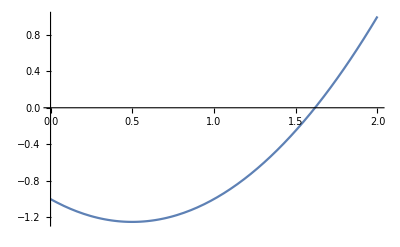

```mathematica
Plot[x^2-x-1,{x,0,2}]
```

```mathematica
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{σ,0.001,1},AxesLabel->{"σ","x*"}]],{r,0.001,1},{k0,0.001,10},{μ,-r,r},{δ,0.001,1},{k,0.001,10},{θ,1,10},{α,0.001,Min[1/k0,θ/k]}]
```

#### - θ

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],θ]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

-(dd1 (p0/r+k δ) (r-μ))/((-1+dd1) k (-k α+θ)^2)

#### - k0

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],k0]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

(dd1 (-(k0 α)/r+(1-k0 α)/r) (r-μ))/((-1+dd1) k (-k α+θ))

```mathematica
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{k0,0.001,1/α-0.001},AxesLabel->{"k0","x*"}],
Epilog->{Black, PointSize[0.02],Point[{{1/(2α) ,xxB[r,μ,σ,θ,1/(2α),α,δ,k]}}]}],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{δ,0.001,1},{k,1,10},{θ,1,10},{α,0.001,1}]
```

#### - α

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],α]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

(dd1 (p0/r+k δ) (r-μ))/((-1+dd1) (-k α+θ)^2)-(dd1 k0^2 (r-μ))/((-1+dd1) k r (-k α+θ))

```mathematica
Simplify[(((k0(1-α k0))/r+k δ) k r-k0^2 (-k α+θ))]
```

k k0+k^2 r δ-k0^2 θ

```mathematica
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{α,0.001,Min[{1/k0,θ/k}]},AxesLabel->{"α","x*"}]],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{δ,0.001,1},{k,0.001,10},{k0,0.001,10},{θ,1,10}]
```

#### - k

```mathematica
D[xxB[r,μ,σ,θ,k0,α,δ,k],k]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0  (1-k0 α)->p0 //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((1/2-μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2)//.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

(dd1 α (p0/r+k δ) (r-μ))/((-1+dd1) k (-k α+θ)^2)+(dd1 δ (r-μ))/((-1+dd1) k (-k α+θ))-(dd1 (p0/r+k δ) (r-μ))/((-1+dd1) k^2 (-k α+θ))

```mathematica
Simplify[(dd1 α (p0/r+k δ) (r-μ))/((-1+dd1) k (-k α+θ)^2)+(dd1 δ (r-μ))/((-1+dd1) k (-k α+θ))-(dd1 (p0/r+k δ) (r-μ))/((-1+dd1) k^2 (-k α+θ))]
```

(dd1 (2 k p0 α+k^2 r α δ-p0 θ) (r-μ))/((-1+dd1) k^2 r (-k α+θ)^2)

```mathematica
Simplify[(α (p0/r+k δ))/(-k α+θ)+δ-(p0/r+k δ)/k]
```

-(2 k p0 α+k^2 r α δ-p0 θ)/(k^2 r α-k r θ)

```mathematica
Solve[2 k p0 α+k^2 r α δ-p0 θ==0,k]
```

{{k→(-p0 α-√(p0^2 α^2+p0 r α δ θ))/(r α δ)},{k→(-p0 α+√(p0^2 α^2+p0 r α δ θ))/(r α δ)}}

```mathematica
kest=(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ);
Manipulate[Show[Plot[xxB[r,μ,σ,θ,k0,α,δ,k],{k,0.001,θ/α-0.001},AxesLabel->{"k","x*"}],
Epilog->{Black, PointSize[0.02],Point[{(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ),xxB[r,μ,σ,θ,k0,α,δ,(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ)]}]}],{r,0.001,1},{σ,0.001,1},{μ,-r,r},{δ,0.001,1},{k0,1,10},{θ,1,10},{α,0.001,1/k0}]
```

## Threshold value x*_C

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[( 1/2-mu/sigma^2)^2+2r/sigma^2];
omega[a_,k0_]:=a k0 (1-a k0);
xx[r_,μ_, σ_,θ_,k0_,α_,δ_]:=(r-μ)/((-1+d1[μ,σ,r]) r θ^2)(d1[μ,σ,r] (δ θ r + 2 omega[α,k0])+Sqrt[r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 omega[α,k0](omega[α,k0]+r δ θ)]);
```

#### - r

```mathematica
D[xx[r,μ,σ,θ,k0,α,δ],r];
```

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],r]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

(dd1 (-2 k0 α (-1+k0 α)+r δ θ)+√ψ)/((-1+dd1) r θ^2)-((r-μ) (dd1 (-2 k0 α (-1+k0 α)+r δ θ)+√ψ))/((-1+dd1) r^2 θ^2)-((r-μ) (dd1 (-2 k0 α (-1+k0 α)+r δ θ)+√ψ))/((1-dd1)^2 r θ^2 √((-1/2+μ/σ^2)^2+(2 r)/σ^2) σ^2)+((r-μ) (dd1 δ θ+(-2 k0 α (-1+k0 α)+r δ θ)/(√((-1/2+μ/σ^2)^2+(2 r)/σ^2) σ^2)+(2 r δ^2 θ^2+4 dd1^2 δ θ ω+(8 dd1 ω (r δ θ+ω))/(√((-1/2+μ/σ^2)^2+(2 r)/σ^2) σ^2))/(2 √ψ)))/((-1+dd1) r θ^2)

```mathematica
Manipulate[Show[Plot[xx[r,μ,σ,θ,k0,α,δ],{r,0.01,Max[{0.001,μ+0.001}]},AxesLabel->{"r","x*"}]],{σ,0.001,1},{k0,0.001,10},{μ,-1,1},{δ,0.001,1},{k,1,10},{θ,1,10},{α,0.001,1/k0}]
```

```mathematica
Manipulate[Show[Plot[xx[r,μ,σ,θ,k0,α,δ],{r,0.01,Max[{0.001,μ+0.001}]},AxesLabel->{"r","x*"}]],{μ,-1,1}]
```

#### - μ

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],μ]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω//. k0 α (-1+k0 α)->-ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

((r-μ) (-1+(2 μ-σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)) (r δ θ+2 ω+(2 (1-(2 μ)/σ^2+ϕ) ω (r δ θ+ω))/(√ψ)))/((-1+dd1) r θ^2 σ^2)-(√ψ+dd1 (r δ θ+2 ω))/((-1+dd1) r θ^2)-((r-μ) (-1/σ^2-(1/2-μ/σ^2)/(√((-1/2+μ/σ^2)^2+(2 r)/σ^2) σ^2)) (√ψ+dd1 (r δ θ+2 ω)))/((1-dd1)^2 r θ^2)

```mathematica
Manipulate[Show[Plot[xx[r,μ,σ,θ,k0,α,δ],{μ,-r,r},AxesLabel->{"μ","x*"}, AxesOrigin->{0,0}]],{r,0.001,1},{σ,0.001,1},{k0,0.001,10},{δ,0.001,2},{k,1,100},{θ,1,10},{α,0.001,1/k0}]
```

#### - σ

```mathematica
D[xx[r,μ,σ,θ,k0,α,δ],σ]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

-((r-μ) ((-(4 r)/σ^3+(4 μ (1/2-μ/σ^2))/σ^3)/(2 √((1/2-μ/σ^2)^2+(2 r)/σ^2))+(2 μ)/σ^3) (√ψ+dd1 (r δ θ+2 ω)))/((-1+dd1)^2 r θ^2)+((r-μ) ((4 dd1 ((-(4 r)/σ^3+(4 μ (1/2-μ/σ^2))/σ^3)/(2 √((1/2-μ/σ^2)^2+(2 r)/σ^2))+(2 μ)/σ^3) ω (r δ θ+ω))/(√ψ)+((-(4 r)/σ^3+(4 μ (1/2-μ/σ^2))/σ^3)/(2 √((1/2-μ/σ^2)^2+(2 r)/σ^2))+(2 μ)/σ^3) (r δ θ+2 ω)))/((-1+dd1) r θ^2)

```mathematica
Solve[-(√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω))+(1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2) (r δ θ+2 ω))+(4 (1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2) ω (r δ θ+ω)/√(r^2 δ^2 θ^2+4 (1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2)^2 ω (r δ θ+ω))+(r δ θ+2 ω))(-1+1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2)==0,σ]
```

$Aborted

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],σ]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

((r-μ) ((2 μ)/σ^3+(-4 μ^2-4 r σ^2+2 μ σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)) ((2 (r δ θ+2 ω+(2 (1-(2 μ)/σ^2+ϕ) ω (r δ θ+ω))/(√ψ)))/(-1-(2 μ)/σ^2+ϕ)-(√ψ+1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω))/((1/2+μ/σ^2-ϕ/2)^2)))/(r θ^2)

```mathematica
Simplify@Expand[(2 (r δ θ+2 ω+(2 (1-(2 μ)/σ^2+ϕ) ω (-r δ θ+ω))/(√ψ)))/(-1-(2 μ)/σ^2+ϕ)-(√ψ+1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω))/((1/2+μ/σ^2-ϕ/2)^2)]
```

-(4 (-4 μ^2 ω^2+4 μ σ^2 ϕ ω^2+σ^4 (ψ+2 √ψ ω+ω^2-ϕ^2 ω^2)+r δ θ (4 μ^2 ω-4 μ σ^2 ϕ ω+σ^4 (√ψ+(-1+ϕ^2) ω))))/((-2 μ+σ^2 (-1+ϕ))^2 √ψ)

```mathematica
Simplify@Expand[-4 μ^2 ω^2+4 μ σ^2 ϕ ω^2+σ^4 (ψ+2 √ψ ω+ω^2-ϕ^2 ω^2)+r δ θ (4 μ^2 ω-4 μ σ^2 ϕ ω+σ^4 (√ψ+(-1+ϕ^2) ω))] (* queremos mostrar que <0 -> derivada >0 *)
```

r δ θ σ^4 √ψ+σ^4 ψ+4 r δ θ μ^2 ω-r δ θ σ^4 ω-4 r δ θ μ σ^2 ϕ ω+r δ θ σ^4 ϕ^2 ω+2 σ^4 √ψ ω-4 μ^2 ω^2+σ^4 ω^2+4 μ σ^2 ϕ ω^2-σ^4 ϕ^2 ω^2

```mathematica
Manipulate[Show[Plot[xx[r,μ,σ,θ,k0,α,δ],{σ,0.001,1},AxesLabel->{"σ","x*"}]],{r,0.001,1},{μ,-r,r},{k0,0.001,1/α-0.001},{δ,0.001,1},{k,1,10},{θ,1,10},{α,0.001,1/k0}]
```

#### - θ

```mathematica
D[xx[r,μ,σ,θ,k0,α,δ],θ]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω//. k0 α (1-k0 α)->ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

-(2 (r-μ) (√ψ+dd1 (r δ θ+2 ω)))/((-1+dd1) r θ^3)+((r-μ) (dd1 r δ+(2 r^2 δ^2 θ+4 dd1^2 r δ ω)/(2 √ψ)))/((-1+dd1) r θ^2)

```mathematica
Simplify[-2  (√ψ+dd1 (r δ θ+2α p0 ))+ θ(dd1 r δ+(2 r^2 δ^2 θ+4 dd1^2 r δ α p0)/(2 √ψ))]
```

(2 dd1^2 p0 r α δ θ+r^2 δ^2 θ^2-dd1 (4 p0 α+r δ θ) √ψ-2 ψ)/(√ψ)

```mathematica
Simplify[-2 (√(r^2 δ^2 θ^2+4 dd1^2  α p0 (r δ θ+α p0))+dd1 (r δ θ+2 α p0))+(dd1 r δ+(2 r^2 δ^2 θ+4 dd1^2 r δ α p0)/(2 √(r^2 δ^2 θ^2+4 dd1^2 α p0 (r δ θ+α p0))))θ]
```

(-r^2 δ^2 θ^2-2 dd1^2 p0 α (4 p0 α+3 r δ θ)-dd1 (4 p0 α+r δ θ) √(r^2 δ^2 θ^2+4 dd1^2 p0 α (p0 α+r δ θ)))/(√(r^2 δ^2 θ^2+4 dd1^2 p0 α (p0 α+r δ θ)))

```mathematica
Simplify[2 dd1^2 p0 r α δ θ+r^2 δ^2 θ^2-dd1 (4 p0 α+r δ θ) √(r^2 δ^2 θ^2+4 dd1^2 α p0 (r δ θ+α p0))-2 r^2 δ^2 θ^2+4 dd1^2 α p0 (r δ θ+α p0)]
```

-r^2 δ^2 θ^2+2 dd1^2 p0 α (2 p0 α+3 r δ θ)-dd1 (4 p0 α+r δ θ) √(r^2 δ^2 θ^2+4 dd1^2 p0 α (p0 α+r δ θ))

```mathematica
Module[{θ=0},
{-r^2 δ^2 θ^2+2 dd1^2 p0 α (2 p0 α+3 r δ θ)-dd1 (4 p0 α+r δ θ) √(r^2 δ^2 θ^2+4 dd1^2 p0 α (p0 α+r δ θ)),-r^2 δ^2 θ^2-2 dd1^2 p0 α (4 p0 α+3 r δ θ)-dd1 (4 p0 α+r δ θ) √(r^2 δ^2 θ^2+4 dd1^2 p0 α (p0 α+r δ θ)), (r^2 δ^2 θ^2+dd1 r δ θ (-√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω))+2 dd1 ω)-2 (r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)+2 dd1 √(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)) ω))}]
```

{4 dd1^2 p0^2 α^2-8 dd1 p0 α √(dd1^2 p0^2 α^2),-8 dd1^2 p0^2 α^2-8 dd1 p0 α √(dd1^2 p0^2 α^2),-2 (4 dd1^2 ω^2+4 dd1 ω √(dd1^2 ω^2))}

```mathematica
1/(√ψ)(r-μ) (r^2 δ^2 θ^2+dd1 r δ θ (-√□+2 dd1 ω)-2 (ψ+2 dd1 √ψ ω))
```

```mathematica
Solve[(r-μ) (r^2 δ^2 θ^2+dd1 r δ θ (-√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω))+2 dd1 ω)-2 (r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)+2 dd1 √(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)) ω))==0,θ]
```

{{θ→0},{θ→-(4 dd1^2 ω)/(r δ)}}

```mathematica
Manipulate[Plot[{(*2  (√(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 α(1-k0 α)k0(r δ θ+α(1-k0 α)k0))+d1[μ,σ,r]  (r δ θ+2 α(1-k0 α)k0))+(d1[μ,σ,r]  r δ+(2 r^2 δ^2 θ+4 d1[μ,σ,r]^2 r δ  α (1-k0 α)k0)/(2 √(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0))))θ*),
r^2 δ^2 θ^2+d1[μ,σ,r] r δ θ (-√(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0))+2 d1[μ,σ,r](1-k0 α)α k0)-2 (r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0)+2 d1[μ,σ,r] √(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0)) (1-k0 α)α k0),
-((2 (r-μ) (√(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0))+d1[μ,σ,r] (r δ θ+2 (1-k0 α)α k0)))/((-1+d1[μ,σ,r]) r θ^3))+((r-μ) (d1[μ,σ,r]r δ+(2 r^2 δ^2 θ+4 d1[μ,σ,r]^2 r δ (1-k0 α)α k0)/(2 √(r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 (1-k0 α)α k0(r δ θ+(1-k0 α)α k0)))))/((-1+d1[μ,σ,r]) r θ^2)}
,{θ,0.001,10},AxesLabel->{"θ","x*"}, AxesOrigin->{0,0}],{r,0.001,1},{σ,0.001,1},{δ,0,1},{k0,1,10},{μ,-r,r},{α,0.001,1/k0}]
```

```mathematica
6
```

```mathematica
Module[{σ=0.005,
μ=0.03,
r=0.05,
δ=2,
α=0.01,
θ=10,
k=100,
k0=90},
dd1=d1[μ,σ,r] ;
ω=(1-k0 α)k0;
(*(2 (3 dd1^2 r δ ω-3 dd1^4 r δ ω+√(-8 dd1^2 r^2 δ^2 ω^2+25 dd1^4 r^2 δ^2 ω^2-26 dd1^6 r^2 δ^2 ω^2+9 dd1^8 r^2 δ^2 ω^2)))/(3 (-r^2 δ^2+dd1^2 r^2 δ^2))*)
3 dd1^2 r δ ω-3 dd1^4 r δ ω+√(-8 dd1^2 r^2 δ^2 ω^2+25 dd1^4 r^2 δ^2 ω^2-26 dd1^6 r^2 δ^2 ω^2+9 dd1^8 r^2 δ^2 ω^2)]
```

-2.3365

```mathematica
N@Sqrt[6]
```

2.44949

```mathematica
Limit[xx[r,μ,σ,θ,k0,α,δ]/(1/θ),θ->Infinity]//.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1
```

((r-μ) (√(r^2 δ^2)+(r δ (-2 μ+σ^2 (1+ϕ)))/(2 σ^2)))/((-1+dd1) r)

```mathematica
Limit[xx[r,μ,σ,θ,k0,α,δ]/(((r-μ) (√(r^2 δ^2)+(r δ (-2 μ+σ^2 (1+ϕ)))/(2 σ^2)))/((-1+dd1) r)/θ),θ->Infinity]//.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1
```

1

```mathematica
Manipulate[Plot[xx[r,μ,σ,θ,k0,α,δ],{θ,0.001,10},AxesLabel->{"θ","x*"}],{r,0.001,1},{σ,0.001,1},{δ,0,1},{k0,1,10},{μ,-r,r},{α,0,1/k0}]
```

#### - k0

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],k0]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (-1+k0 α)->-ω//. k0 α (1-k0 α)->ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

(α (-1+2 k0 α) (r-μ) (-2 μ+σ^2 (1+ϕ)) (-2 σ^2+((-2 k0 α+2 k0^2 α^2-r δ θ) (-2 μ+σ^2 (1+ϕ)))/(√ψ)))/(2 (-1+dd1) r θ^2 σ^4)

#### - α

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],α]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

(k0 (-1+2 k0 α) (r-μ) (-2 μ+σ^2 (1+ϕ)) (-2 σ^2+((-2 k0 α+2 k0^2 α^2-r δ θ) (-2 μ+σ^2 (1+ϕ)))/(√ψ)))/(2 (-1+dd1) r θ^2 σ^4)

#### - δ

```mathematica
Simplify[D[xx[r,μ,σ,θ,k0,α,δ],δ]]//. 1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

((r-μ) (dd1 r θ+(2 r^2 δ θ^2+4 dd1^2 r θ ω)/(2 √ψ)))/((-1+dd1) r θ^2)

## Comparative plots x*B and x*C

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
```

```mathematica
1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2
```

1.6662

```mathematica
If[1-α k0>0 && θ-α k>0 && r-μ>0, Print["Suposições verificadas."],Print["Não avançar!"]];
```

Suposições verificadas.

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
omega[a_,k0_]:=a k0 (1-a k0);
xxB[r_,μ_, σ_,θ_,k0_,α_,δ_,k_]:=d1[μ,σ,r]/(-1+d1[μ,σ,r])( δ  k + (1-  α k0)k0/r  )/(θ- α k) (r-μ)/k;
xx[r_,μ_, σ_,θ_,k0_,α_,δ_]:=(r-μ)/((-1+d1[μ,σ,r]) r θ^2)(d1[μ,σ,r] (δ θ r + 2 omega[α,k0])+Sqrt[r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 omega[α,k0](omega[α,k0]+r δ θ)]); (*igual a xPos*)
```

```mathematica
xPos[r_,μ_, σ_,θ_,k0_,α_,δ_]:=1/((-1+d1[μ,σ,r]) r θ^2)(-d1[μ,σ,r] (-2 k0 α+2 k0^2 α^2-r δ θ) (r-μ)+√((r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 k0 α (-1+k0 α) (-k0 α+k0^2 α^2-r δ θ)) (r-μ)^2));
```

#### - r

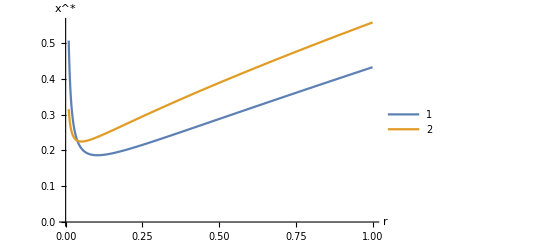

```mathematica
μ=0.01; σ=0.9;
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{r,μ,1},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"r","x^*"}]
```

#### - μ

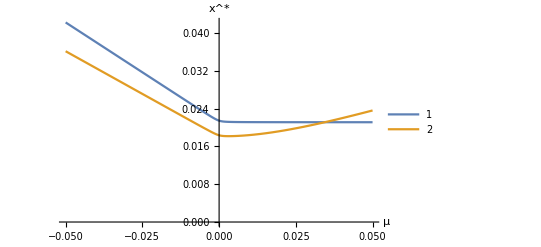

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{μ,-r,r},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"μ","x^*"}]
```

#### - σ

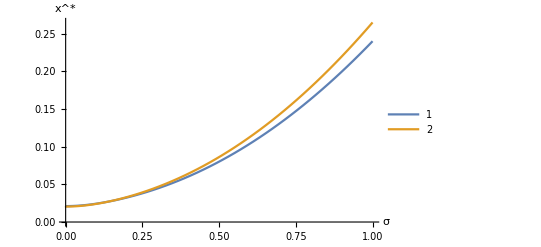

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{σ,0,1},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"σ","x^*"}]
```

```mathematica
Solve[(x^2-3x+1)/(x-1)^2==0,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

```mathematica
N@3+√5
```

5.23607

```mathematica
Solve[1-x/(x-1)^2==0,x]
```

{{x→1/2 (3-√5)},{x→1/2 (3+√5)}}

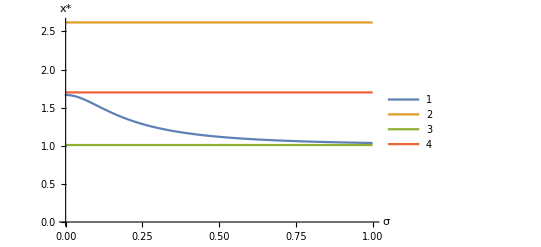

```mathematica
Show[Plot[{d1[μ,σ,r],1/2(3+Sqrt[5]),1.01,1.7},{σ,0,1},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"σ","x*"}]
```

#### - θ

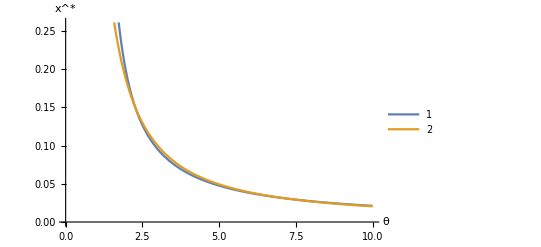

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{θ,α*k,10},AxesOrigin->{0,0},PlotLegends->"Placeholder",AxesOrigin->{0,0}],AxesLabel->{"θ","x^*"}]
```

#### - k0

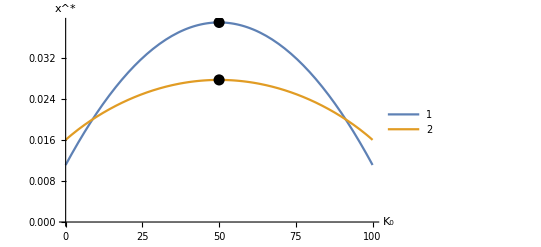

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{k0,0,1/α},PlotLegends->"Placeholder",AxesOrigin->{0,0}],
Epilog->{Black, PointSize[0.02],Point[{{1/(2α) ,xxB[r,μ,σ,θ,1/(2α),α,δ,k]}}],
(*Point[{1/(2α) ,xNeg[r,μ,σ,θ,1/(2α),α,δ]}],*)
Point[{{1/(2α) ,xPos[r,μ,σ,θ,1/(2α),α,δ]}}]
},
AxesLabel->{"K_0","x^*"}]
```

#### - k

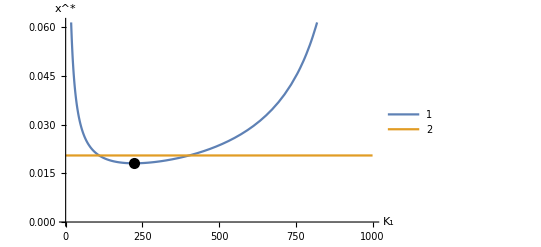

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{k,0,θ/α},PlotLegends->"Placeholder",AxesOrigin->{0,0}],
Epilog->{Black, PointSize[0.02],Point[{(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ),xxB[r,μ,σ,θ,k0,α,δ,(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ)]}]},
AxesLabel->{"K_1","x^*"}]
```

```mathematica
(-k0(1-α k0)α+√((k0(1-α k0))^2 α^2+k0(1-α k0)r α δ θ))/(r α δ)
```

223.209

#### - α

```mathematica
k/k0^2 (k0+k r δ)
```

1.23457

```mathematica
θ=1;
θ>k/k0^2 (k0+k r δ)
```

False

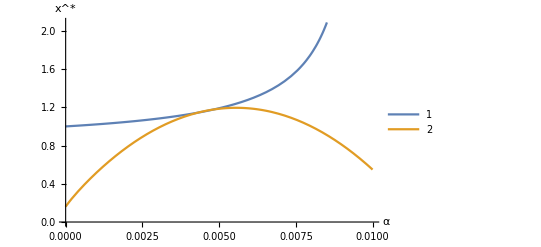

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{α,0,Min[1/k0,θ/k]},PlotLegends->"Placeholder",AxesOrigin->{0,0}],
AxesLabel->{"α","x^*"}]
```

```mathematica
θ=10;
θ>k/k0^2 (k0+k r δ)
```

True

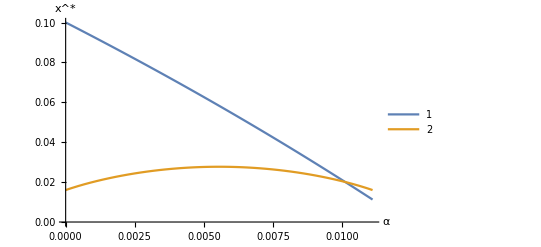

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{α,0,Min[1/k0,θ/k]},PlotLegends->"Placeholder",AxesOrigin->{0,0}],
AxesLabel->{"α","x^*"}]
```

#### - δ

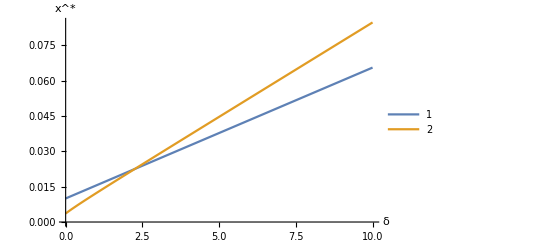

```mathematica
Show[Plot[{xxB[r,μ, σ,θ,k0,α,δ,k],xPos[r,μ, σ,θ,k0,α,δ]},{δ,0,10},PlotLegends->"Placeholder",AxesOrigin->{0,0}],
AxesLabel->{"δ","x^*"}]
```

## Optimal capacity K*(x*)

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
```

```mathematica
K[r_,μ_, σ_,θ_,k0_,α_,δ_,x_]:=θ/(2 α)-(δ (r-μ))/(2 x α);
```

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
omega[a_,k0_]:=a k0 (1-a k0);
```

```mathematica
xx[r_,μ_, σ_,θ_,k0_,α_,δ_]:=(r-μ)/((-1+d1[μ,σ,r]) r θ^2)(d1[μ,σ,r] (δ θ r + 2 omega[α,k0])+Sqrt[r^2 δ^2 θ^2+4 d1[μ,σ,r]^2 omega[α,k0](omega[α,k0]+r δ θ)]);
```

```mathematica
K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.k0 (1-a k0)->pi0
```

θ/(2 α)-((-1+dd1) r δ θ^2)/(2 α (dd1 (2 k0 α (1-k0 α)+r δ θ)+√(r^2 δ^2 θ^2+4 dd1^2 k0 α (1-k0 α) (k0 α (1-k0 α)+r δ θ))))

```mathematica
θ/(2 α)-((-1+dd1) r δ θ^2)/(2 α (dd1 (2  α pi0+r δ θ)+√(r^2 δ^2 θ^2+4 dd1^2 α (pi0) (α (pi0)+r δ θ))))
```

```mathematica
Simplify[D[θ/(2 α)-((-1+dd1) r δ θ^2)/(2 α (dd1 (r δ θ+2 ω)+√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)))),dd1]]
```

((-1+dd1) r δ θ^2 (r δ θ+2 ω+(4 dd1 ω (r δ θ+ω))/(√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)))))/(2 α (dd1 (r δ θ+2 ω)+√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)))^2)-(r δ θ^2)/(2 α (dd1 (r δ θ+2 ω)+√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω))))

```mathematica
Simplify[(dd1 (r δ θ+2 ω)+√(r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)))-(-1+dd1) r δ θ]
```

r δ θ+2 dd1 ω+√(r^2 δ^2 θ^2+4 dd1^2 r δ θ ω+4 dd1^2 ω^2)

#### - r

```mathematica
D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],r]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

-((-1+dd1) δ θ^2)/(2 α (√ψ+dd1 (r δ θ+2 ω)))-(r δ θ^2)/(2 α √((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2 (√ψ+dd1 (r δ θ+2 ω)))+((-1+dd1) r δ θ^2 (dd1 δ θ+(r δ θ+2 ω)/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2)+(2 r δ^2 θ^2+4 dd1^2 δ θ ω+(8 dd1 ω (r δ θ+ω))/(√((1/2-μ/σ^2)^2+(2 r)/σ^2) σ^2))/(2 √ψ)))/(2 α (√ψ+dd1 (r δ θ+2 ω))^2)

```mathematica
Manipulate[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{r,0.01,Max[{0.001,μ+0.001}]},AxesLabel->{"r","K*"}],{σ,0.001,1},{k0,0.001,10},{μ,-1,1},{δ,0.001,1},{k,1,10},{θ,1,10},{α,0.001,1/k0}]
```

```mathematica
μ=0.01; σ=0.9;
```

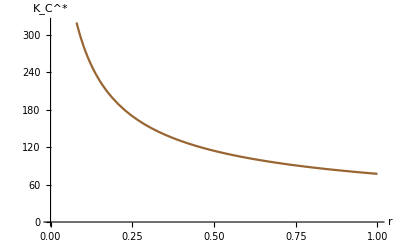

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{r,μ,1},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"r","K_C^*"}]
```

#### - μ

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],μ]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

((-1+dd1) r δ θ^2 (-1+(2 μ-σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^2)) (r δ θ+2 ω+(2 (1-(2 μ)/σ^2+ϕ) ω (r δ θ+ω))/(√ψ)))/(2 α σ^2 (√ψ+dd1 (r δ θ+2 ω))^2)-(r δ θ^2 (-1/σ^2-(1/2-μ/σ^2)/(√((-1/2+μ/σ^2)^2+(2 r)/σ^2) σ^2)))/(2 α (√ψ+dd1 (r δ θ+2 ω)))

```mathematica
Manipulate[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{μ,-r,r},AxesLabel->{"μ","K*"}],{σ,0.001,1},{k0,0.001,10},{r,0.001,1},{δ,0.001,1},{θ,1,10},{α,0.001,1/k0}]
```

```mathematica
μ=-r
K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]]
```

-0.05

223.278

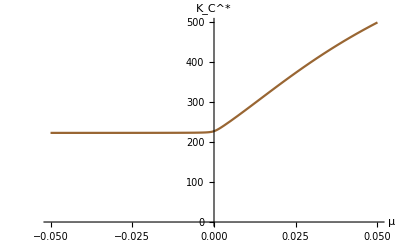

```mathematica
Show[Plot[{K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]]},{μ,-r,r},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"μ","K_C^*"}]
```

#### - σ

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],σ]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

(r δ θ^2 ((2 μ)/σ^3+(-4 μ^2-4 r σ^2+2 μ σ^2)/(√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2) σ^5)) (-√ψ-1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω)+1/2 (-1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω+(2 (1-(2 μ)/σ^2+ϕ) ω (r δ θ+ω))/(√ψ))))/(2 α (√ψ+1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω))^2)

```mathematica
Manipulate[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{σ,0.001,1},AxesLabel->{"σ","K*"}],{k0,0.001,10},{r,0.001,1},{μ,-r,r},{δ,0.001,1},{θ,1,10},{α,0.001,1/k0}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

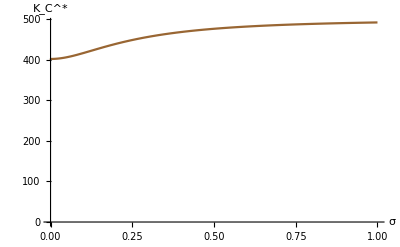

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{σ,0,1},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"σ","K_C^*"}]
```

#### - θ

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],θ]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

1/(2 α)-((-1+dd1) r δ θ)/(α (√ψ+dd1 (r δ θ+2 ω)))+((-1+dd1) r δ θ^2 (dd1 r δ+(2 r^2 δ^2 θ+4 dd1^2 r δ ω)/(2 √ψ)))/(2 α (√ψ+dd1 (r δ θ+2 ω))^2)

```mathematica
Simplify[(√ψ+dd1 (r δ θ+2 ω))-2(-1+dd1) r δ θ]
```

-(-2+dd1) r δ θ+√ψ+2 dd1 ω

```mathematica
Simplify@Expand[α (√ψ+dd1 (r δ θ+2 ω))^2-2(-1+dd1) r δ θ (√ψ+dd1 (r δ θ+2 ω))+(-1+dd1) r δ θ^2 (dd1 r δ+(2 r^2 δ^2 θ+4 dd1^2 r δ ω)/(2 √ψ))]
```

((-1+dd1) r^3 δ^3 θ^3+2 r (1+dd1 (-1+α)) δ θ √ψ (√ψ+2 dd1 ω)+α √ψ (√ψ+2 dd1 ω)^2+dd1 r^2 δ^2 θ^2 ((1+dd1 (-1+α)) √ψ+2 (-1+dd1) dd1 ω))/(√ψ)

```mathematica
Simplify[2 r (1+dd1 (-1+α)) δ θ  (√ψ+2 dd1 ω)+dd1 r^2 δ^2 θ^2 (1+dd1 (-1+α))]
```

r (1+dd1 (-1+α)) δ θ (dd1 r δ θ+2 √ψ+4 dd1 ω)

```mathematica
Limit[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]]/θ, θ->Infinity] //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ
```

((r δ+√(r^2 δ^2)) σ^2)/(α (2 √(r^2 δ^2) σ^2+r δ (-2 μ+σ^2 (1+ϕ))))

```mathematica
Manipulate[Plot[{K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],(r δ+√(r^2 δ^2)) σ^2/α (2 √(r^2 δ^2) σ^2+r δ (-2 μ+σ^2 (1+√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2))))θ}
,{θ,1,100},AxesLabel->{"θ","K*"}],{r,0.001,1},{μ,-r,r-0.001},{σ,0.001,1},{k0,1,10},{α,0.001,1/k0},{δ,0,1}]
```

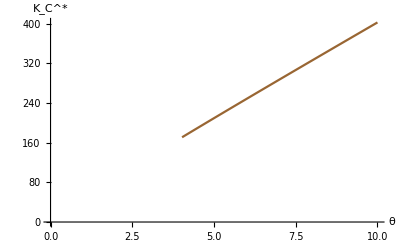

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{θ,K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]]*α,10},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"θ","K_C^*"}]
```

#### - k0

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],k0]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

-(r (-1+2 k0 α) δ θ^2 (-2 μ+σ^2 (-1+ϕ)) (-2 μ+σ^2 (1+ϕ)))/(2 σ^2 (-4 k0 α μ+4 k0^2 α^2 μ-2 r δ θ μ+2 k0 α σ^2-2 k0^2 α^2 σ^2+r δ θ σ^2+2 k0 α σ^2 ϕ-2 k0^2 α^2 σ^2 ϕ+r δ θ σ^2 ϕ+2 σ^2 √ψ) √ψ)

```mathematica
Manipulate[Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{k0,1,1/α},AxesLabel->{"k0","K*"}],
Epilog->{Black, PointSize[0.02],Point[{1/(2α),K[r,μ,σ,θ,1/(2α),α,δ,xx[r,μ,σ,θ,1/(2α),α,δ]] }]}],
{r,0.001,1},{μ,-r,r-0.001},{σ,0.001,1},{θ,1,10},{α,0.001,1},{δ,0,1}]
```

```mathematica
1/(2α)
```

50.

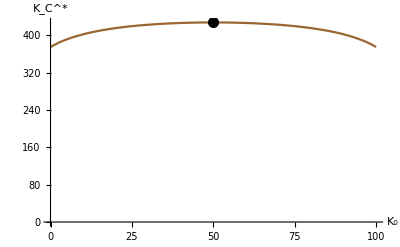

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{k0,0,1/α},AxesOrigin->{0,0},PlotStyle->Brown],
Epilog->{Black, PointSize[0.02],Point[{1/(2α),K[r,μ,σ,θ,1/(2α),α,δ,xx[r,μ,σ,θ,1/(2α),α,δ]] }]},
AxesLabel->{"K_0","K_C^*"}]
```

#### - α

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],α]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

-θ/(2 α^2)-(k0 r (-1+2 k0 α) δ θ^2 (-2 μ+σ^2 (-1+ϕ)) (-2 μ+σ^2 (1+ϕ)))/(2 α σ^2 (-4 k0 α μ+4 k0^2 α^2 μ-2 r δ θ μ+2 k0 α σ^2-2 k0^2 α^2 σ^2+r δ θ σ^2+2 k0 α σ^2 ϕ-2 k0^2 α^2 σ^2 ϕ+r δ θ σ^2 ϕ+2 σ^2 √ψ) √ψ)+((-1+dd1) r δ θ^2)/(2 α^2 (√ψ+dd1 (r δ θ+2 ω)))

```mathematica
Simplify[-θ(√ψ+dd1 (r δ θ+2 ω))+(-1+dd1) r δ θ^2]
```

-θ (r δ θ+√ψ+2 dd1 ω)

```mathematica
Manipulate[Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{α,0.001,1/k0},AxesLabel->{"α","K*"}],
Epilog->{Black, PointSize[0.02],Point[{1/(2k0),K[r,μ,σ,θ,k0,1/(2 k0),δ,xx[r,μ,σ,θ,k0,1/(2 k0),δ]] }]}],
{r,0.001,1},{μ,-r,r-0.001},{σ,0.001,1},{θ,1,10},{k0,1,10},{δ,0,1}]
```

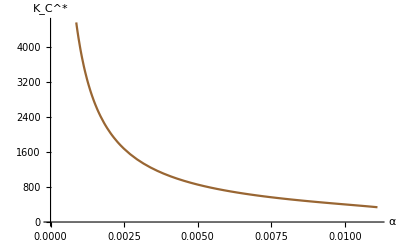

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{α,0,1/k0},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"α","K_C^*"}]
```

#### - δ

```mathematica
Simplify[D[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],δ]]//.1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. 1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2-> dd1 //. k0 α (1-k0 α)->ω //. k0 α (-1+k0 α)->-ω//.-1/2+√((1/2-μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.-1/2+√((-1/2+μ/σ^2)^2+(2 r)/σ^2)-μ/σ^2->dd1-1//.1/2-√((-1/2+μ/σ^2)^2+(2 r)/σ^2)+μ/σ^2->-dd1+1 //.√((-1/2+μ/σ^2)^2+(2 r)/σ^2)->(dd1-1/2+μ/σ^2) //.√(1+(4 μ^2)/σ^4+(8 r)/σ^2-(4 μ)/σ^2)->ϕ //. r^2 δ^2 θ^2+4 dd1^2 ω (r δ θ+ω)->ψ
```

(r θ^2 (-1-(2 μ)/σ^2+ϕ) (-√ψ-1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω)+δ (1/2 r θ (1-(2 μ)/σ^2+ϕ)+(r θ (r δ θ+1/2 (1-(2 μ)/σ^2+ϕ)^2 ω))/(√ψ))))/(4 α (√ψ+1/2 (1-(2 μ)/σ^2+ϕ) (r δ θ+2 ω))^2)

```mathematica
Manipulate[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{δ,1,10},AxesLabel->{"δ","K*"}],{r,0.001,1},{μ,-r,r-0.001},{σ,0.001,1},{θ,1,10},{k0,1,10},{α,0.001,1/k0}]
```

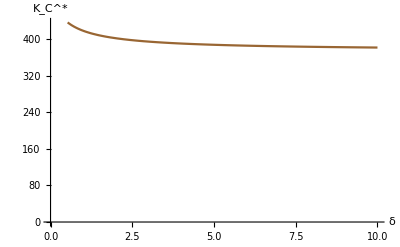

```mathematica
Show[Plot[K[r,μ,σ,θ,k0,α,δ,xx[r,μ,σ,θ,k0,α,δ]],{δ,0,10},AxesOrigin->{0,0},PlotStyle->Brown],AxesLabel->{"δ","K_C^*"}]
```

## Δ parâmetros

```mathematica
σ=0.005;
μ=0.03;
r=0.05;
δ=2;
α=0.01;
θ=10;
k=100;
k0=90;
```

```mathematica
K[r_,μ_, σ_,θ_,k0_,α_,δ_,x_]:=θ/(2 α)-(δ (r-μ))/(2 x α);
```

```mathematica
d1[mu_,sigma_,r_]:=1/2-mu/sigma^2+Sqrt[(1/2-mu/sigma^2)^2+2r/sigma^2];
omega[a_,k0_]:=a k0 (1-a k0);
```

```mathematica
Δ={0.005,0.05,0.1,0.15,0.2,0.25,0.3};
Grid[{ Prepend[Δ,"σ"],
Prepend[Map[Function[σ,xxB[r,μ,σ,θ,k0,α,δ,k]],Δ],"x_B"],
Prepend[Map[Function[σ,xPos[r,μ,σ,θ,k0,α,δ]],Δ], "x_C"],
Prepend[Map[Function[σ,K[r,μ,σ,θ,k0,α,δ,xPos[r,μ,σ,θ,k0,α,δ]]],Δ], "K*(x_C)"]
},
Dividers->{{2->True},{1->True,2->True,-1->True}}
]
```

σ | 0.005 | 0.05 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3
x_B | 0.0211199 | 0.0219684 | 0.0243435 | 0.0279206 | 0.0325177 | 0.0380669 | 0.0445543
x_C | 0.0204838 | 0.0214187 | 0.024042 | 0.0280056 | 0.0331132 | 0.0392905 | 0.0465218
K*(x_C) | 402.362 | 406.624 | 416.812 | 428.586 | 439.601 | 449.097 | 457.009

```mathematica
Δ={-r,-0.01,0.01,r-0.00001};
Grid[{ Prepend[Δ,"μ"],
Prepend[Map[Function[μ,xxB[r,μ,σ,θ,k0,α,δ,k]],Δ],"x_B"],
Prepend[Map[Function[μ,xPos[r,μ,σ,θ,k0,α,δ]],Δ], "x_C"],
Prepend[Map[Function[μ,K[r,μ,σ,θ,k0,α,δ,xPos[r,μ,σ,θ,k0,α,δ]]],Δ], "K*(x_C)"]
},
Dividers->{{2->True},{1->True,2->True,-1->True}}
]
```

μ | -0.05 | -0.01 | 0.01 | 0.04999
x_B | 0.0422328 | 0.0253648 | 0.0211374 | 0.0211164
x_C | 0.0361374 | 0.021704 | 0.0184016 | 0.0236042
K*(x_C) | 223.278 | 223.553 | 282.628 | 499.958

```mathematica
Δ={-r,-0.01,0.01,r-0.00001};
Grid[{ Prepend[Δ,"μ"],
Prepend[Map[Function[δ,xxB[r,μ,σ,θ,k0,α,δ,k]],Δ],"x_B"],
Prepend[Map[Function[δ,xPos[r,μ,σ,θ,k0,α,δ]],Δ], "x_C"],
Prepend[Map[
Function[μ,
If[xxB[r,μ,σ,θ,k0,α,δ,k]>xPos[r,μ,σ,θ,k0,α,δ],
aB[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,k]* xxB[r,μ,σ,θ,k0,α,δ,k]^d1[μ,σ,r],
hC[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,σ,θ,k0,α,δ,Kopt[xxB[r,μ,σ,θ,k0,α,δ,k],r,μ,θ,α,δ]]]
],Δ], "F(x_B)"],
Prepend[Map[
Function[μ,
hC[xPos[r,μ,σ,θ,k0,α,δ],r,μ,σ,θ,k0,α,δ,Kopt[xPos[r,μ,σ,θ,k0,α,δ],r,μ,θ,α,δ]]
],Δ], "F(x_C)"],
Prepend[Map[Function[δ,K[r,μ,σ,θ,k0,α,δ,xPos[r,μ,σ,θ,k0,α,δ]]],Δ], "K*(x_C)"]
},
Dividers->{{2->True},{1->True,2->True,-1->True}}
]
```

μ | -0.05 | -0.01 | 0.01 | 0.04999
x_B | 0.00972627 | 0.00994859 | 0.0100597 | 0.010282
x_C | 0.00308833 | 0.003501 | 0.00370111 | 0.00409183
F(x_B) | 0.094976267796 | 0.47207138306 | 95.5908 | 5.27792×10^6
F(x_C) | 0.1566 | 0.779049 | 187.473 | 5.89987×10^6
K*(x_C) | 516.19 | 502.856 | 497.298 | 487.783